Nathan Magari                                      (CELL 1)
805505312
natemagari@g.ucla.edu
HW1

(CELL 2) My computer programming experience is limited, but I took PIC 10-A last year and was introduced to C++ and I have also learned Python through the Physics 4AL and 4BL labs. I have used Matlab briefly but I have never tried using Mathematica.

```mathematica
(*CELL 3*)
Remove["Global`*"] 
a = 16;
b = 0.25;
ab = 22;
Print["a is ",a]   (* This line will output the value of a *)
Print["b is ",b]  (* This line will output the value of b *)
Print["ab is ", ab] (* This line will output the value of ab which is not the same as a*b, it is its own separate label*)
Print[HoldForm[ab/(a b)]," = ",HoldForm[ab/(a·b)]," is ",ab/(a b)] (* This line will compute ab/(a*b) == 22/(16*0.25)== 5.5 and output that value*)
Print["Remember that 'ab' does not equal 'a times b' since there is no space between."]
```

a is 16

b is 0.25

ab is 22

ab/(a b) = ab/(a·b) is 5.5

Remember that 'ab' does not equal 'a times b' since there is no space between.

```mathematica
(*CELL 4*)
Remove["Global`*"] 
Print[Factor[540 a^4−1017 a^3*b−834 a^2*b^2+653 a*b^3−70 b^4]]
```

(3 a-7 b) (12 a-5 b) (15 a-2 b) (a+b)

```mathematica
(*CELL 5*)
Remove["Global`*"] 
Print[HoldForm[Sin[θ]Cos [φ]+Sin [φ] Cos[θ]==Sin [θ+φ]]," is ",Simplify[Sin[θ]Cos [φ]+Sin [φ] Cos[θ]]==Sin [θ+φ]]
```

Sin[θ] Cos[φ]+Sin[φ] Cos[θ]==Sin[θ+φ] is True

```mathematica
(*CELL 6*)
Print[HoldForm[(6.35^0.2-12.6*(2.6*10^7)^0.25)/(7.6*10^-5)^3]," = ",ScientificForm[Evaluate[(6.35^0.2-12.6*(2.6*10^7)^0.25)/(7.6*10^-5)^3],4]]
```

(6.35^0.2-12.6 (2.6 10^7)^0.25)/((7.6/10^5)^3) = -2.046×10^15

```mathematica
(*CELL 7*)
Remove["Global`*"] 
(*   Part i   *)
Print["PART I"]
a = -1.5`16*10^-7;
b = 5`16*10^9;
c = - 500`16;
x[t_] = a t^2 + b t + c;
t1 = (-b + (b^2-4a c)^0.5)/(2 a);
t2  = (-b - (b^2-4a c)^0.5)/(2a);
Print["Solution 1: t1 = ",t1]
Print ["Solution 2: t2 = ",t2]
(*   Part ii   *)
Print["PART II"]
vave[t_] = (x[t]-x[0])/t;
Print["Average velocity from  t = 0 to t = t1: ",vave[t1]]
Print["Average velocity from  t = 0 to t = t2: ",vave[t2]]
Print["Oops, we are getting an indeterminate expression because t1 is so small that it was evaluated as 0"]
(*   Part iii   *)
Print["PART III"]
Print["Let's find a better way to assign t1 and t2 by modifying the quadratic formula"]
t1 = 2c/(-b - (b^2-4a c)^0.5);
t2 =(-b - (b^2-4a c)^0.5)/(2a);
Print[]
Print["Solution 1: t1 = ",t1]
Print ["Solution 2: t2 = ",t2]
Print [ "Now we have evaluated the small root using an equivalent expression to the quadratic formula which was achieved by multiplying by the conjugate of the numerator: ",HoldForm[t1 = 2c/(-b - (b^2-4a c)^0.5)]]
Print [ "The larger root is still calculated using: ", HoldForm[t2 =(-b - (b^2-4a c)^0.5)/(2a)]]
Print["Now the average velocities should not be indeterminate"]
Print["Average velocity from  t = 0 to t = t1: ",vave[t1]]
Print["Average velocity from  t = 0 to t = t2: ",vave[t2]]
```

PART I

Solution 1: t1 = 0.

Solution 2: t2 = 3.33333×10^16

PART II

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Average velocity from  t = 0 to t = t1: Indeterminate

Average velocity from  t = 0 to t = t2: 0.

Oops, we are getting an indeterminate expression because t1 is so small that it was evaluated as 0

PART III

Let's find a better way to assign t1 and t2 by modifying the quadratic formula

Solution 1: t1 = 1.×10^-7

Solution 2: t2 = 3.33333×10^16

Now we have evaluated the small root using an equivalent expression to the quadratic formula which was achieved by multiplying by the conjugate of the numerator: t1=(2 c)/(-b-(b^2-4 a c)^0.5)

The larger root is still calculated using: t2=(-b-(b^2-4 a c)^0.5)/(2 a)

Now the average velocities should not be indeterminate

Average velocity from  t = 0 to t = t1: 5.×10^9

Average velocity from  t = 0 to t = t2: 0.

```mathematica
(*CELL 8*)
Remove["Global`*"]
A={{a,b,c},{d,e,f},{g,h,i}};
B ={{j,k,l},{m,n,o},{p,q,r}};
Print[HoldForm[Transpose[A.B] == Transpose[B].Transpose[A]]," is ", Simplify[Transpose[A.B]] == Transpose[B].Transpose[A]]
Print[HoldForm[Inverse[A.B] == Inverse[B].Inverse[A]]," is ", Simplify[Inverse[A.B]] == Simplify[Inverse[B].Inverse[A]]]
```

Transpose[A.B]==Transpose[B].Transpose[A] is True

Inverse[A.B]==Inverse[B].Inverse[A] is True

PART I

The position is: {-Cos[t]-t Sin[t]+t Sin[π/6+t],-t Cos[t]+t Cos[π/6+t]+Sin[t]}

The velocity is: {-t Cos[t]+t Cos[π/6+t]+Sin[π/6+t],Cos[π/6+t]+t Sin[t]-t Sin[π/6+t]}

The acceleration is: {-Cos[t]+2 Cos[π/6+t]+t Sin[t]-t Sin[π/6+t],t Cos[t]-t Cos[π/6+t]+Sin[t]-2 Sin[π/6+t]}

PART II

Angle between a and v at t = 3 is 1.0626 radians

PART III

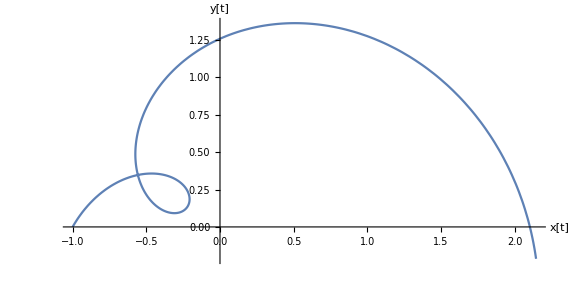

```mathematica
(*CELL 9*)
Remove["Global`*"]
Print["PART I"]
r[t_]:={(t Sin [t+π/6]−t Sin [t]−Cos [t]),(Sin [t]−t Cos [t]+t Cos [t+π/6])};
v[t_]:= r'[t];
a[t_]:= v'[t];
Print["The position is: ", r[t]]
Print["The velocity is: ", v[t]]
Print["The acceleration is: ", a[t]]
theta[t_] := ArcCos[v[t].a[t]/(Norm[v[t]]*Norm[a[t]])];
Print["PART II"]
Print["Angle between a and v at t = 3 is ", N[FullSimplify[theta[3]]], " radians"]
Print["PART III"]
ParametricPlot[r[t],{t,0,6}, ImageSize->Large,AxesLabel->{"x[t]","y[t]"}]
```